# Ensemble excitation

Want to excite an atom to a Rydberg state near deterministically, given an ensemble of atoms loaded into a dipole trap.

```mathematica
constsdir="..\\constants\\";
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
```

## setup and test

```mathematica
(*prob of speed v at temp T*)
MaxBoltzDist[T_,v_]:=PDF[MaxwellDistribution[√((kB T)/mRb)],v];

MaxBoltzSpeedSample[T_,speedband_,samples_]:=Module[
{fmax,y,v,vdomain=speedband,f=0,flist={},vlist={},ylist={},samps=0},
fmax=MaxBoltzDist[T,√((kB T)/mRb)]; 
While [samps<samples,
v = (vdomain[[2]]-vdomain[[1]])RandomReal[];
f =MaxBoltzDist[T,v];
y=fmax RandomReal[];
If[y≤f,
AppendTo[ylist,y];(*prob that y<=f is prob that speed is measured*)
AppendTo[vlist,v];(*speeds*)
AppendTo[flist,f];(*probabilities*)
samps++;
];
];
{vlist,ylist,flist}
];

MaxBoltzVelocitySample[T_,speedband_,samples_]:=Module[{velocityList={},ex,ey,ez,v,A},
For[n=1,n<samples+1,n++,
ex=2 RandomReal[]-1;
ey=2 RandomReal[]-1;
ez=2 RandomReal[]-1;
v=MaxBoltzSpeedSample[T,speedband,1][[1,1]];
A=√(ex^2+ey^2+ez^2);
AppendTo[velocityList,{ex v/A,ey v/A,ez v/A}];
];
velocityList
];
```

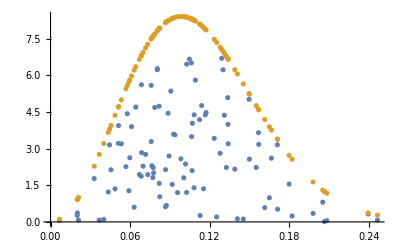

```mathematica
(*test Maxwell-Boltzmann sampling*)
{v,y,f}=MaxBoltzSpeedSample[5*^-5,{0,1},100];
ListPlot[{Transpose@{v,y},Transpose@{v,f}}]
```

```mathematica
MaxBoltzVelocitySample[5*^-5,{0,1},10]
```

{{0.0746331,-0.124351,0.049859},{-0.0435147,0.0330007,0.163811},{0.0300022,0.0210011,-0.0328762},{0.0354189,0.0433296,-0.0562395},{0.0619439,-0.0191179,-0.0529433},{0.130466,-0.106329,-0.127489},{-0.0840778,-0.0779752,-0.0668379},{-0.113374,0.0243405,-0.0398124},{0.00295118,0.13463,-0.150942},{-0.08228,-0.0691214,-0.0215349}}

## stationary atoms

See “Creating single-atom and single-photon sources from entangled atomic ensembles”, Saffman & Walker.

```mathematica
Pwstate = 1/(1+((n-1)^2 Ω^2)/(4 n Δ^2));
```

```mathematica
nSteps = Range[1,50];
ΔSteps={1,2,5,10,20}*10^6;
Ω=5*^5;
data = {};
For[i=1,i<Length[ΔSteps]+1,i++,
AppendTo[data,Array[{n,Pwstate/.Δ-> ΔSteps[[i]]}/.n-> nSteps[[#]]&,Length[nSteps]]]
]
```

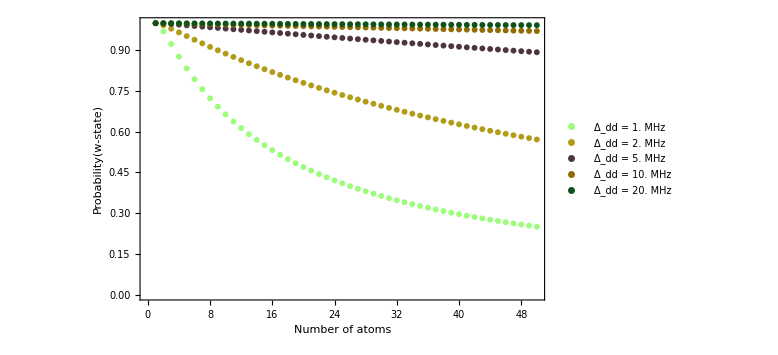

```mathematica
ListPlot[data,LabelStyle->Directive[Black,Medium],Axes->Off,Frame->{True,True,False,False},FrameLabel->{"Number of atoms","Probability(w-state)"},PlotStyle->Array[RGBColor[RandomReal[],RandomReal[],RandomReal[]]&,steps],PlotLegends->Array[StringForm["Δ_dd = `` MHz",NumberForm[ΔSteps[[#]]*1*^-6//N,2]]&,Length[ΔSteps]],ImageSize->Large]
```

## atoms in a dipole trap

```mathematica
zR = (π w0FORT^2)/λ;
ωr = 1/w0FORT √((2kB TFORT)/mRb);
ωz = 1/zR √((2kB TFORT)/mRb);
σr = 1/ωr √((kB T)/mRb);
σz = 1/ωr √((kB T)/mRb);
```

```mathematica
λ = 1.064*^-6;
w0FORT = 2.5*^-6;
TFORT = 1*^-3;
```

How likely is it to find an atom within a slice of the dipole trap of width 2*wz?

```mathematica
tempTable =Table[T,{T,10*^-6,100*^-6,10*^-6}] ;
steps = Length[tempTable];
data = {};
For[i=1,i<steps+1,i++,
AppendTo[data ,Evaluate[Table[{wz,Integrate[1/(2π σr σz)Exp[-1/2(r^2/σr^2+z^2/σz^2)]r/.T-> tempTable[[i]],{r,0,w0FORT},{z,-wz,wz}]}, {wz,100*^-9,2*^-6 ,50*^-9}]]];
]
```

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

General::stop: Further output of NumberForm::sigz will be suppressed during this calculation.

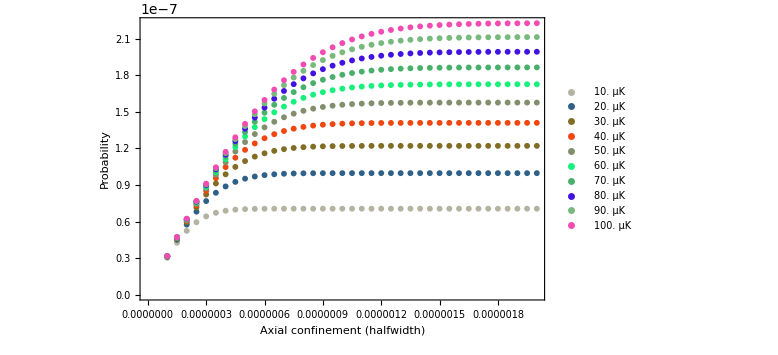

```mathematica
ListPlot[data,LabelStyle->Directive[Black,Medium],Axes->Off,Frame->{True,True,False,False},FrameLabel->{"Axial confinement (halfwidth)","Probability"},PlotStyle->Array[RGBColor[RandomReal[],RandomReal[],RandomReal[]]&,steps],PlotLegends->Array[StringForm["`` μK",NumberForm[tempTable[[#]]*1*^6//N,2]]&,steps],ImageSize->Large]
```

What is the mean spacing of atoms in a dipole trap? Consider a case in which the trap width is the same in both r and z (say, by superposing two orthogonal trap beams)

```mathematica
λ = 1.064*^-6;
w0FORT = 2.5*^-6;
TFORT = 1*^-3;
Tatom = 40*^-6;
```

```mathematica
Integrate[(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2))/(4 π^2 σr^2 σz^2)Exp[-((x1^2+y1^2)/(2 σr^2)+z1^2/(2 σz^2))]Exp[-((x2^2+y2^2)/(2 σr^2)+z2^2/(2 σz^2))],{x1,-∞,∞},{y1,-∞,∞},{z1,-∞,∞},{x2,-∞,∞},{y2,-∞,∞},{z2,-∞,∞}]
```

$Aborted

```mathematica
data = Table[StandardDeviation[RandomVariate[ProbabilityDistribution[1/(2π σr^2)Exp[-r^2/σr^2]/.T->Tatom,{r,-∞,∞}],10]]&,steps]
```

{-1.65395×10^-12,8.79097×10^-13,1.0162×10^-12,-1.51078×10^-12,2.56776×10^-13,-4.81236×10^-13,-1.96904×10^-12,-1.66174×10^-12,-2.05887×10^-12,2.31023×10^-12}

```mathematica
MeanSeparation[list_]:=Mean[Abs[list[[i]] -  list[[j]]]]
```

```mathematica
list={1,2,5,6};
combos ={};
For[i=1,i<Length[list],i++,
For[j=i,j<Length[list],j++,
AppendTo[combos,{i,j}]
]
]
```

```mathematica
combos
```

{{1,1},{1,2},{1,3},{2,2},{2,3},{3,3}}

```mathematica
[Flatten[Table[If[i≠j,{i,j}],{i,1,Length[list]},{j,i,Length[list]}],1],]
```

{Null,{1,2},{1,3},{1,4},Null,{2,3},{2,4},Null,{3,4},Null}